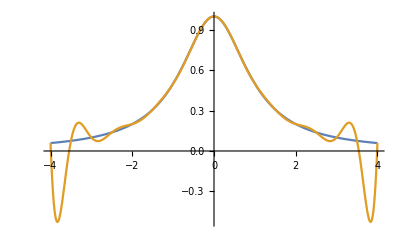

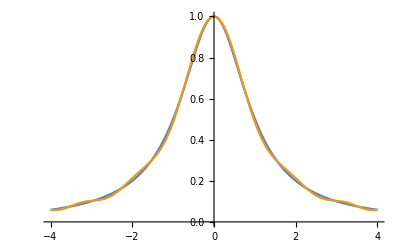

```mathematica
(*HW1: Compute the 20-order interpolation function of f(x)=(x^2_1)^{-1} in [-5,5]*)
f[x_]:=(x^2+1)^{-1}
arr = Array[Flatten[{#,f[#]}] &,21,{-5,5}];(*equal length*)
arr2 = Table[Flatten[{N[5Cos[i π/20]],f[N[5Cos[i π/20]]]}],{i,0,20}]; (*Chebyshev*)
lagrange = FullSimplify[InterpolatingPolynomial[arr,x]];
lagrange2 = InterpolatingPolynomial[arr2,x];
Plot[{f[x],lagrange},{x,-4,4}]
Plot[{f[x],lagrange2},{x,-4,4}]
```

```mathematica
px =Array[#&,21,{-5,5}];
px2= Table[N[5Cos[i π/20]],{i,0,20}]; 
(*My Lagrange function*)
l[px_]:=Sum[Product[If[j≠i,x-px[[j]]],{j,1,21}]/Product[If[j≠i,px[[i]]-px[[j]]],{j,1,21}] f[px[[i]]],{i,1,21}];
Plot[{f[x],l[px]},{x,-4,4}]
Plot[{f[x],l[px2]},{x,-4,4}]
```

-Graphics-

-Graphics-